```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20]
```

```mathematica
RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20},16]
```

{imp8,imp10,imp3,imp7,imp19,imp5,imp12,imp9,imp16,imp20,imp4,imp11,imp17,imp18,imp14,imp2}

```mathematica
p[z_]:=ListLinePlot[Table[{x,y},{x,Range[1,20,1]},{y,Range[1,20,1]}][[z]],PlotStyle->Gray]
```

```mathematica
line[z_]:=ListLinePlot[Table[{x,z},{x,Range[1,20,0.01]}],PlotStyle->Gray]
```

```mathematica
line1[z_]:=ListLinePlot[Table[{x,z},{x,Range[0,21,0.01]}],PlotStyle->Blue]
```

```mathematica
p1[z_]:=ListLinePlot[Table[{x,y},{x,Range[1,20,1]},{y,Range[0,21,1]}][[z]],PlotStyle->Blue]
```

```mathematica
ab=Module[{list={RandomSample[{imp01,imp02,imp03,imp04,imp05,imp06,imp07,imp08,imp09,imp10,imp11,imp12,imp00,imp00,imp00,imp00,imp00,imp00,imp00,imp00}]}},
aa=Module[{},
Table[ToExpression[StringTake[StringCases[ToString[list],WordCharacter..][[x]],-2]],{x,20}]];
listn1=Transpose[Join[{Range[1,20,1]},{aa}]];listn2=Sort[Transpose[Join[{aa},{Range[1,20,1]}]]];
{listn1,listn2}]
```

{{{1,0},{2,3},{3,8},{4,0},{5,11},{6,0},{7,10},{8,0},{9,7},{10,4},{11,0},{12,2},{13,1},{14,0},{15,0},{16,12},{17,0},{18,9},{19,5},{20,6}},{{0,1},{0,4},{0,6},{0,8},{0,11},{0,14},{0,15},{0,17},{1,13},{2,12},{3,2},{4,10},{5,19},{6,20},{7,9},{8,3},{9,18},{10,7},{11,5},{12,16}}}

```mathematica
Clear[l30, l20, im1, im2, im3, im4, im5, im6, im7, im8, im9, im10, im11, im12, im13, im14, im15, im16, im17, 
  im19, im19, im20]
RandomSample[{im1, im2, im3, im4, im5, im6, im7, im8, im9, im10, im11, im12, im13, im14, im15, im16, im17, im19, 
   im19, im20}]
{im9, im15, im20, im2, im17, im16, im8, im14, im11, im12, im6, im4, im19, im7, im10, im1, im3, im13, im5, im19}
Flatten[Table[Position[aa, ToExpression[Table[StringJoin["im", ToString[x], ""], {x, 20}][[y]]]], {y, 20}]]
{19, 4, 13, 7, 5, 2, 10, 3, 15, 9, 18, 11, 16, 17, 6, 12}
Table[StringJoin["im", ToString[z], ""], 
  {z, Flatten[Table[Position[Flatten[Table[Position[aa, ToExpression[Table[StringJoin["im", ToString[x], ""], 
            {x, 20}][[y]]]], {y, 20}]], z], {z, 20}]]}]
{"im9", "im15", "im20", "im2", "im17", "im16", "im8", "im14", "im11", "im12", "im6", "im4", "im18", "im7", 
  "im10", "im1", "im3", "im13", "im5", "im19"}
ToExpression[Out[461]]
{im9, im15, im20, im2, im17, im16, im8, im14, im11, im12, im6, im4, im18, im7, im10, im1, im3, im13, im5, im19}
```

```mathematica
Clear[imp,imp9,imp15,imp20,imp2,imp17,imp16,imp8,imp14,imp11,imp12,imp6,imp4,imp18,imp7,imp10,imp1,imp3,imp13,imp5,imp19]
aa=RandomSample[{imp13,imp1,imp18,imp16,imp17,imp10,imp11,imp14,imp12,imp8,imp15,imp19,imp2,imp9,imp7,imp5,imp6,imp3,imp20,imp4}]
```

{imp12,imp4,imp2,imp19,imp9,imp8,imp5,imp18,imp10,imp14,imp6,imp1,imp11,imp16,imp15,imp3,imp20,imp17,imp7,imp13}

```mathematica
Position[aa,imp2]
Position[aa,imp6]
Position[aa,imp13]
Position[aa,imp18]
```

{{3}}

{{11}}

{{20}}

{{8}}

```mathematica
bb=Flatten[Table[Position[Flatten[Table[Position[aa,ToExpression[Table["imp"<>ToString[x]<>"",{x,20}][[y]]]],{y,20}]],z],{z,20}]]
```

{12,4,2,19,9,8,5,18,10,14,6,1,11,16,15,3,20,17,7,13}

```mathematica
Length[bb]
```

20

```mathematica
leftright:= Transpose[Join[{Range[1,20,1]},{bb}]]
cc:=Flatten[Table[Position[bb,x],{x,Range[1,20,1]}]]
ToExpression[Table["imp"<>ToString[z]<>"",{z,cc}]]
downup= Transpose[Join[{cc},{Range[1,20,1]}]]
```

{imp12,imp3,imp16,imp2,imp7,imp11,imp19,imp6,imp5,imp9,imp13,imp1,imp20,imp10,imp15,imp14,imp18,imp8,imp4,imp17}

{{12,1},{3,2},{16,3},{2,4},{7,5},{11,6},{19,7},{6,8},{5,9},{9,10},{13,11},{1,12},{20,13},{10,14},{15,15},{14,16},{18,17},{8,18},{4,19},{17,20}}

```mathematica
testhori[ϵ1_,ϵ_,m_,y_,x_]:=Module[{Tin=T[1,m],T1=T[1,m],list,tra(*,im1=imp1[ω,ϵ1,m],im2=imp2[ω,ϵ1,m],im3=imp3[ω,ϵ1,m],im4=imp4[ω,ϵ1,m],im5=imp5[ω,ϵ1,m],im6=imp6[ω,ϵ1,m],im7=imp7[ω,ϵ1,m],im8=imp8[ω,ϵ1,m],im9=imp9[ω,ϵ1,m],im10=imp10[ω,ϵ1,m],im11=imp11[ω,ϵ1,m],im12=imp12[ω,ϵ1,m],im13=imp13[ω,ϵ1,m],im14=imp14[ω,ϵ1,m],im15=imp15[ω,ϵ1,m],im16=imp16[ω,ϵ1,m],im17=imp17[ω,ϵ1,m],im18=imp18[ω,ϵ1,m],im19=imp19[ω,ϵ1,m],im20=imp20[ω,ϵ1,m]*)},imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{2,2},{12,12}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{6,6},{17,17}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{13,13},{8,8}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]];
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{15,15}}->ω+ⅈ*0.0001-ϵ1]]];
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{16,16}}->ω+ⅈ*0.0001-ϵ1]]];
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{17,17}}->ω+ⅈ*0.0001-ϵ1]]];
imp18:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{18,18},{5,5}}->ω+ⅈ*0.0001-ϵ1]]];
imp19:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{19,19}}->ω+ⅈ*0.0001-ϵ1]]];
imp20:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{20,20}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
tra[start_,stop_]:=Module[{},
list={{imp12,imp4,imp2,imp19,imp9,imp8,imp5,imp18,imp10,imp14,imp6,imp1,imp11,imp16,imp15,imp3,imp20,imp17,imp7,imp13}};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,start,stop}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
m1=Table[{ω,tra[1,5]},{ω,Range[0,4,0.01]}];
m2=Table[{ω,tra[6,10]},{ω,Range[0,4,0.01]}];
m3=Table[{ω,tra[11,15]},{ω,Range[0,4,0.01]}];
m4=Table[{ω,tra[16,20]},{ω,Range[0,4,0.01]}];
υ1=Module[{},
ρ2:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];
υ2=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];
υ3=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];
υ4=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];{υ1,υ2,υ3,υ4}]
```

```mathematica
testverti[ϵ1_,ϵ_,m_,y_,x_]:=Module[{Tin=T[1,m],T1=T[1,m](*,1=RandomInteger[{1,10}], 2=RandomInteger[{1,10}], 3=RandomInteger[{11,20}], 4=RandomInteger[{11,20}],5=RandomInteger[{1,20}], 6=RandomInteger[{1,20}], 7=RandomInteger[{1,20}],8=RandomInteger[{1,20}], 9=RandomInteger[{1,20}], 10=RandomInteger[{1,20}], 11=RandomInteger[{1,20}],12=RandomInteger[{1,20}], 13=RandomInteger[{1,20}], 14=RandomInteger[{1,20}]*),list,tra(*,im1=imp1[ω,ϵ1,m],im2=imp2[ω,ϵ1,m],im3=imp3[ω,ϵ1,m],im4=imp4[ω,ϵ1,m],im5=imp5[ω,ϵ1,m],im6=imp6[ω,ϵ1,m],im7=imp7[ω,ϵ1,m],im8=imp8[ω,ϵ1,m],im9=imp9[ω,ϵ1,m],im10=imp10[ω,ϵ1,m],im11=imp11[ω,ϵ1,m],im12=imp12[ω,ϵ1,m],im13=imp13[ω,ϵ1,m],im14=imp14[ω,ϵ1,m],im15=imp15[ω,ϵ1,m],im16=imp16[ω,ϵ1,m],im17=imp17[ω,ϵ1,m],im18=imp18[ω,ϵ1,m],im19=imp19[ω,ϵ1,m],im20=imp20[ω,ϵ1,m]*)},imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{7,7},{8,8}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{8,8},{20,20}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{12,12},{3,3}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]];
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{15,15}}->ω+ⅈ*0.0001-ϵ1]]];
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{16,16}}->ω+ⅈ*0.0001-ϵ1]]];
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{17,17},{11,11}}->ω+ⅈ*0.0001-ϵ1]]];
imp18:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{18,18}}->ω+ⅈ*0.0001-ϵ1]]];
imp19:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{19,19}}->ω+ⅈ*0.0001-ϵ1]]];
imp20:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{20,20}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
tra[start_,stop_]:=Module[{},
list={{imp6,imp15,imp5,imp17,imp14,imp19,imp10,imp3,imp16,imp7,imp8,imp1,imp18,imp2,imp12,imp13,imp9,imp11,imp20,imp4}};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,start,stop}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
m1=Table[{ω,tra[1,5]},{ω,Range[0,4,0.01]}];
m2=Table[{ω,tra[6,10]},{ω,Range[0,4,0.01]}];
m3=Table[{ω,tra[11,15]},{ω,Range[0,4,0.01]}];
m4=Table[{ω,tra[16,20]},{ω,Range[0,4,0.01]}];
υ1=Module[{},
ρ2:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];
υ2=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];
υ3=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];
υ4=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];{υ1,υ2,υ3,υ4}]
```

```mathematica
testhori[0.5,0,20,0,3.8]
verti=testverti[0.5,0,20,0,3.8]
Table[Position[hori[[x]],Min[hori[[x]]]],{x,4}]
Table[Position[verti[[x]],Min[verti[[x]]]],{x,4}]
```

{{0.0240844,0.01875,0.0164185,0.0145085,0.012172,0.0102441,0.00973041},{0.0237781,0.0208543,0.0189373,0.0150323,0.0111986,0.0103018,0.0111096},{0.0427372,0.035456,0.032967,0.0290006,0.0221352,0.0154371,0.0132797},{0.0405351,0.0309425,0.0241195,0.0195283,0.0157789,0.0132168,0.0122409}}

{{0.0515316,0.0440192,0.0379425,0.0310043,0.0247908,0.0215931,0.021149},{0.0336354,0.0276167,0.0245998,0.0193418,0.0126538,0.00893056,0.00897646},{0.0413386,0.0307149,0.0239983,0.0192728,0.0147065,0.012029,0.0130664},{0.0204747,0.0149194,0.00982069,0.00618833,0.00503918,0.00725482,0.00982696}}

{{{5}},{{5}},{{6}},{{5}}}

{{{7}},{{6}},{{6}},{{5}}}

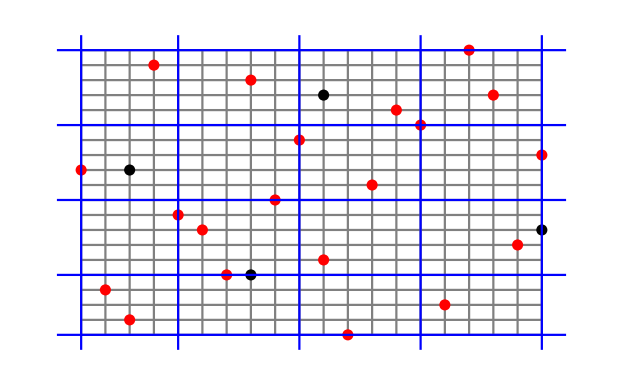

```mathematica
Show[Show[Table[p[z],{z,20}],Table[line[z],{z,20}],ListPlot[leftright,PlotStyle->Red],ListPlot[{{3,12},{11,17},{20,8},{8,5}},PlotStyle->Black],PlotRange->All],Show[line1[1],line1[5],line1[10],line1[15],line1[20],PlotRange->All],Show[p1[1],p1[5],p1[10],p1[15],p1[20],PlotRange->All],Axes->False]
```

```mathematica
{imp12,imp3,imp16,imp2,imp7,imp11,imp19,imp6,imp5,imp9,imp13,imp1,imp20,imp10,imp15,imp14,imp18,imp8,imp4,imp17}
```

```mathematica
bb
```

{12,14,8,20,3,1,10,11,17,7,18,15,16,5,2,9,4,13,6,19}

```mathematica
leftright
```

{{1,6},{2,14},{3,12},{4,18},{5,5},{6,10},{7,9},{8,20},{9,15},{10,8},{11,16},{12,13},{13,4},{14,19},{15,11},{16,7},{17,17},{18,3},{19,2},{20,1}}

```mathematica
leftright= Transpose[Join[{Range[1,20,1]},{bb}]]
```

```mathematica
{{2,8},{3,14},{4,15},{5,17},{6,7},{7,20},{8,1},{9,4},{11,5},{12,3},{13,9},{14,19},{15,11},{17,13},{18,18},{19,16}}
```

{{2,8},{3,14},{4,15},{5,17},{6,7},{7,20},{8,1},{9,4},{11,5},{12,3},{13,9},{14,19},{15,11},{17,13},{18,18},{19,16}}